```mathematica
Needs["ErrorBarPlots`"]
data=Import["~/univ/bsp-cg/out-mats-imbalance/data.csv"]
```

{{0.1,0.156163},{0.1,0.155182},{0.1,0.155238},{0.3,0.166306},{0.3,0.167629},{0.3,0.167936},{0.6,0.161317},{0.6,0.160873},{0.6,0.160046},{0.6,0.160776},{0.8,0.214812},{0.8,0.214949},{0.8,0.214583},{1.,0.241685},{1.,0.243592},{1.,0.243999}}

```mathematica
groups=Gather[data,#1[[1]]==#2[[1]]&]
```

{{{0.1,0.156163},{0.1,0.155182},{0.1,0.155238}},{{0.3,0.166306},{0.3,0.167629},{0.3,0.167936}},{{0.6,0.161317},{0.6,0.160873},{0.6,0.160046},{0.6,0.160776}},{{0.8,0.214812},{0.8,0.214949},{0.8,0.214583}},{{1.,0.241685},{1.,0.243592},{1.,0.243999}}}

```mathematica
groups[[1]]
```

{{0.1,0.156163},{0.1,0.155182},{0.1,0.155238}}

```mathematica
withErrors=Table[{Mean[groups[[i]]],ErrorBar[StandardDeviation[groups[[i]]][[2]]]},{i,1,Length[groups]}]
```

{{{0.1,0.155528},ErrorBar[0.000550927]},{{0.3,0.16729},ErrorBar[0.000866168]},{{0.6,0.160753},ErrorBar[0.000526901]},{{0.8,0.214781},ErrorBar[0.000184917]},{{1.,0.243092},ErrorBar[0.00123537]}}

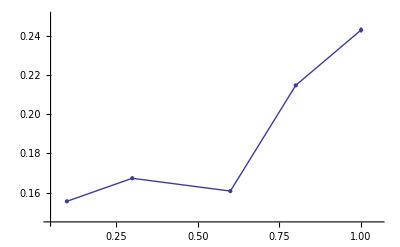

```mathematica
ErrorListPlot[withErrors,Joined->True, Mesh->All, PlotRange->{{0.05,1.05},{0.145,.25}}]
```